```mathematica
Transpose@eegStandardLengthYes[[1]]//ListLinePlot
```

$Aborted

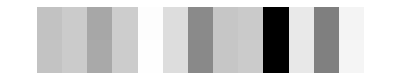

```mathematica
ArrayPlot[%]
```

```mathematica
eegStandardLengthYes[[1]]//Dimensions
```

{13,5101}

```mathematica
Transpose@eegStandardLengthYes[[1]]//Dimensions
```

{5101,13}

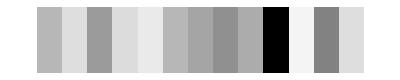

```mathematica
Take[Transpose@eegStandardLengthYes[[1]],{300}]//ArrayPlot
```

```mathematica
Animate[Take[Transpose@eegStandardLengthYes[[1]],{Floor@x}]//ArrayPlot,{x,1,5101}]
```

```mathematica
Animate[Take[Transpose@eegStandardLengthYes[[2]],{Floor@x}]//ArrayPlot,{x,1,5101}]
```

```mathematica
Animate[Take[Transpose@eegStandardLengthNo[[1]],{Floor@x}]//ArrayPlot,{x,1,5101}]
```

```mathematica
Animate[Take[Transpose@eegStandardLengthNo[[2]],{Floor@x}]//ArrayPlot,{x,1,5101}]
```